#### Homework 3 - Nikola Totev | FN 62271 | Group 6

```mathematica
(*Exercise 1*)
```

```mathematica
dividedDiff[nodes_,vals_]:=(If[Length[nodes]==1,vals[[1]],((dividedDiff[nodes[[2;;Length[nodes]]],vals[[2;;Length[nodes]]]]-dividedDiff[nodes[[1;;Length[nodes]-1]],vals[[1;;Length[nodes]-1]]])/(nodes[[Length[nodes]]]-nodes[[1]]))]);
newtonPoly[nodes_, values_, x_] := (values[[1]]+Sum[dividedDiff[nodes[[1;;n]], values[[1;;n]]]*Product[x-nodes[[i]],{i,1,n-1}], {n, 2, Length[nodes]}]);
```

```mathematica
f[x_] = 1/(1+25 x^2);
```

```mathematica
approximateRunge[n_,x_]:=
(
nodes=Table[i,{i,-1,1, N[2/n]}];

	conditionTable = Table
	[
		If[i==Length[nodes],
		x≥ nodes[[i-1]] && x≤ nodes[[i]],
		x≥ nodes[[i-1]] && x<nodes[[i]]] ,

	{i, 2, Length[nodes]}
	];

	values = Table
	[
		newtonPoly
		[
			{nodes[[i-1]],(nodes[[i-1]]+nodes[[i]])/2, nodes[[i]]}, (*Node list*)
			{f[nodes[[i-1]]], f[(nodes[[i-1]]+nodes[[i]])/2],f[nodes[[i]]]}, (*Value list*)
			x (*Variable*)
		],

              {i,2,Length[nodes]} (*Table itteration info*)
	];

	Piecewise[Transpose[{values,conditionTable}]]
);
```

Approximation at n = 1

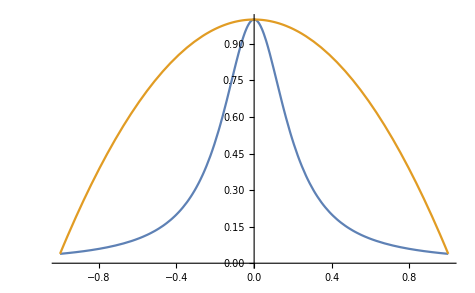
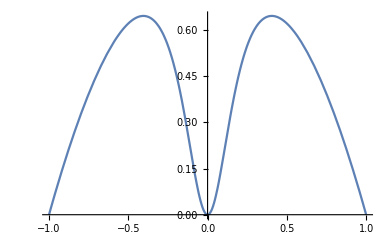
```mathematica
nOne[x_] = approximateRunge[1, x];
funcPlotAtOne = Plot[{f[x], nOne[x]}, {x,-1,1}];

errOne [x_] = f[x]-nOne[x];
errorPlotAtOne = Plot[Abs[errOne[x]], {x,-1,1}];

(*Function plot*)
Show[funcPlotAtOne]
-Graphics-

(*Absolute Error plot*)
Show[errorPlotAtOne]
-Graphics-
```

Approximation at n = 5

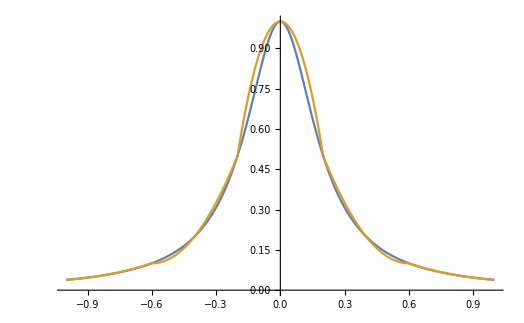
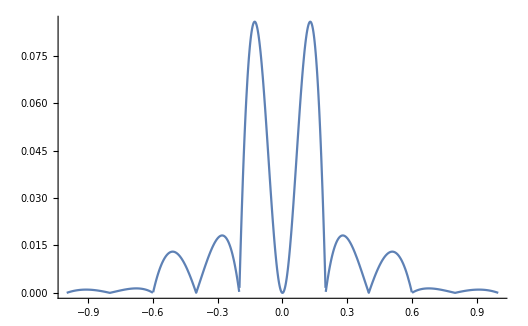
```mathematica
nFive[x_] = approximateRunge[5, x];
funcPlotAtFive = Plot[{f[x], nFive[x]}, {x,-1,1}];

errFive [x_] = f[x]-nFive[x];
errorPlotAtFive= Plot[Abs[errFive[x]], {x,-1,1},PlotRange->All];

(*Function plot*)
Show[funcPlotAtFive]
-Graphics-


(*Absolute Error plot*)
Show[errorPlotAtFive]
-Graphics-
```

Approximation at n = 15

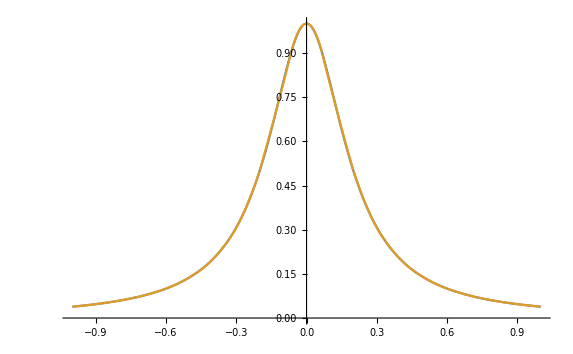
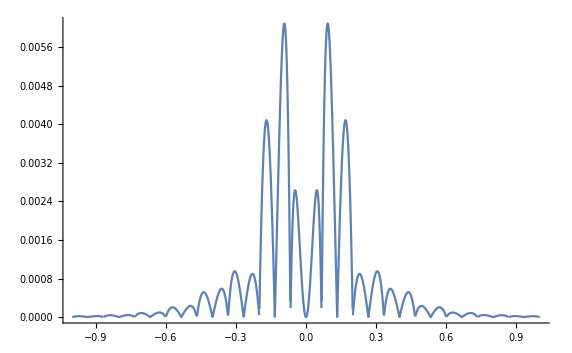
```mathematica
nFifteen[x_] = approximateRunge[15, x];
funcPlotAtFifteen= Plot[{f[x], nFifteen[x]}, {x,-1,1}];

errFifteen [x_] = f[x]-nFifteen[x];
errorPlotAtFifteen= Plot[Abs[errFifteen[x]], {x,-1,1}, PlotRange->All];

(*Function plot*)
Show[funcPlotAtFifteen]
-Graphics-

(*Absolute Error plot*)
Show[errorPlotAtFifteen]
-Graphics-
```

Approximation at n = 30

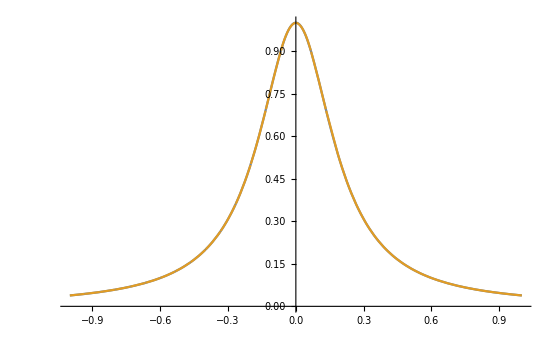
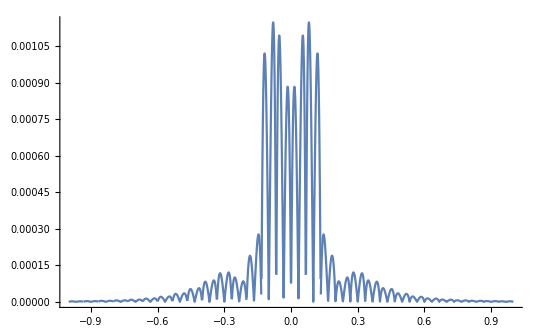
```mathematica
nThirty[x_] = approximateRunge[30, x];
funcPlotAtThirty= Plot[{f[x], nThirty[x]}, {x,-1,1}];

errThirty [x_] = f[x]-nThirty[x];
errorPlotAtThirty= Plot[Abs[errThirty[x]], {x,-1,1}, PlotRange->All];

(*Function plot*)
Show[funcPlotAtThirty]
-Graphics-

(*Absolute Error plot*)
Show[errorPlotAtThirty]
-Graphics-
```

Approximation at n = 200

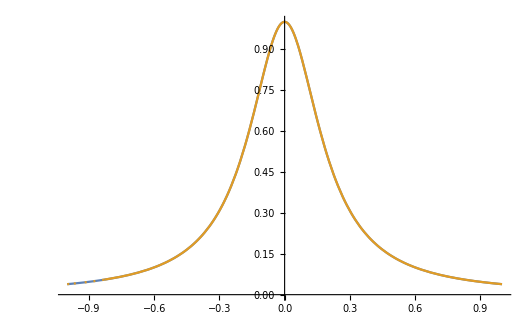
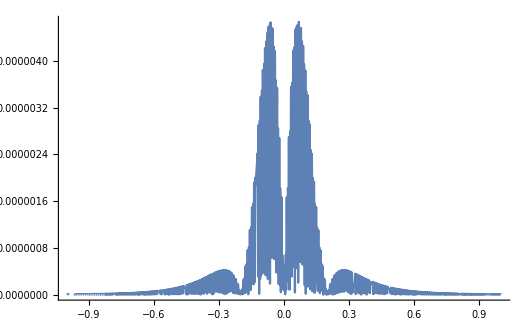
```mathematica
n200[x_] = approximateRunge[200, x];
funcPlotAt200= Plot[{f[x], n200[x]}, {x,-1,1}];

err200[x_] = f[x]-n200[x];
errorPlotAt200= Plot[Abs[err200[x]], {x,-1,1}, PlotRange->All];

(*Function plot*)
Show[funcPlotAt200]
-Graphics-

(*Absolute Error plot*)
Show[errorPlotAt200]
-Graphics-
```

```mathematica
(*Exercise 2*)
```

```mathematica
seconds={0,1,2,3,4,5,6,7,8,9};
height={450,445,431,408,375,332,279,216,143,61};
baseFunc[x_]=a x^2+b x+c;
```

```mathematica
sumFunc[a_,b_,c_]=∑_(i=1)^Length[seconds] (a seconds⟦i⟧^2+b seconds⟦i⟧+c-height⟦i⟧)^2;
```

```mathematica
DerivativeA[a_,b_,c_]=D[sumFunc[a,b,c], a];
DerivativeB[a_,b_,c_]=D[sumFunc[a,b,c], b];
DerivativeC[a_,b_,c_]=D[sumFunc[a,b,c], c];
```

```mathematica
coefs=Solve[{DerivativeA[a,b,c]==0,DerivativeB[a,b,c]==0,DerivativeC[a,b,c]==0},{a,b,c}];

coefs
{{a->-647/132,b->127/132,c->4943/11}}
```

```mathematica
substituedBaseFunc[x_]=baseFunc[x]/.coefs[[1]];

substituedBaseFunc[x]
4943/11+(127 x)/132-(647 x^2)/132
```

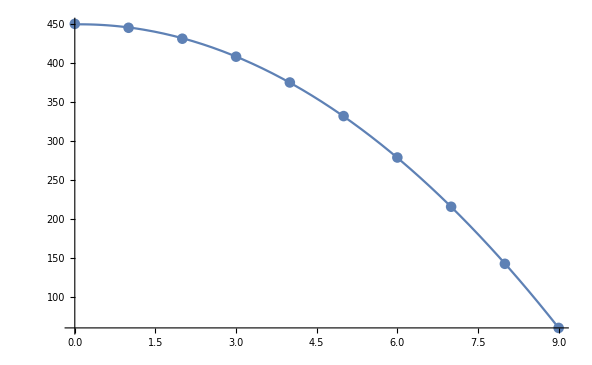
```mathematica
funcPlot=Plot[substituedBaseFunc[x],{x,0,9}];
heightPlot=ListPlot[Transpose[{seconds,height}]];

Show[{funcPlot,heightPlot}]
-Graphics-
```

```mathematica
(*Exercise 3*)
```

```mathematica
nodes = {1, 2, 3,4,5};
values = {1,2,4,10,31};
```

```mathematica
baseFunc[x_]=a x^2+b x+c;
```

```mathematica
sumFunc[a_,b_,c_]=∑_(i=1)^Length[nodes] (a nodes⟦i⟧^2+b nodes⟦i⟧+c-values⟦i⟧)^2;
```

```mathematica
DerivativeA[a_,b_,c_]=D[sumFunc[a,b,c], a];
DerivativeB[a_,b_,c_]=D[sumFunc[a,b,c], b];
DerivativeC[a_,b_,c_]=D[sumFunc[a,b,c], c];
```

```mathematica
coefs=Solve[{DerivativeA[a,b,c]==0,DerivativeB[a,b,c]==0,DerivativeC[a,b,c]==0},{a,b,c}];
```

```mathematica
coefs
{{a->22/7,b->-422/35,c->56/5}}
```

```mathematica
substituedBaseFunc[x_]=baseFunc[x]/.coefs[[1]];

substituedBaseFunc[x]
56/5-(422 x)/35+(22 x^2)/7
```

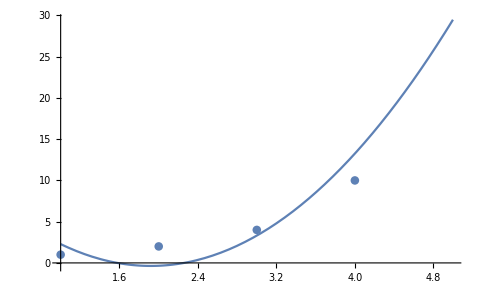
```mathematica
funcPlot=Plot[substituedBaseFunc[x],{x, 1,5}];
nodePlot = ListPlot[Transpose[{nodes,values}]];

Show[{funcPlot,nodePlot}]
-Graphics-
```